## Data

```mathematica
(* Initialize stuff *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Load and extract data *)
```

```mathematica
vrad =SemanticImport["vrad_simu_challenge_0.rdb",ExcludedLines->{2}];
```

```mathematica
data =Normal@vrad[All,#]&/@ {"jdb",(#"rv_planet"+#"rv_inst_noise")1000&,(#"sig_rv"*1000)^2 &};
```

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,logP_,logK_]:=Module[{f,K=Exp[logK],P=Exp[logP]},
f = 2 Pi (FractionalPart[data[[1]]/P]+phi);
rv = K Cos[f]
]
chi2[phi_?NumericQ,logP_?NumericQ,logK_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,logP,logK];
Total[(data[[2]]- rv)^2/data[[3]]]
]
```

```mathematica
(* Try a test *)
```

```mathematica
chi2[0.75,Log[16.0],Log[1.5]]
```

531.207

```mathematica
Clear[plot1,plot2];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
plot2[logK_,phi_,st_:Red]:= Plot[Exp[logK]Cos[2 Pi (t + phi)],{t,0,1},PlotStyle->st]
```

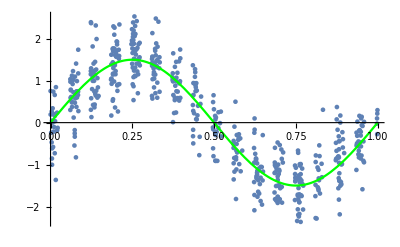

```mathematica
Show[plot1[Log[16]],plot2[Log[1.5],0.75,Green]]
```

## Fisher Matrix

```mathematica
f1=D[chi2[x,y,z],{{x,y,z},2}]/.{x-> 0.75,y->Log[16.0],z->Log[1.5]}//Diagonal
```

{169791.,3.08037×10^7,5257.15}

```mathematica
1/Sqrt[f1/2]
```

{0.00343209,0.000254808,0.0195047}

```mathematica
Needs["NumericalCalculus`"];
```

```mathematica
ND[ND[chi2[x,y,Log[1.5]],y,Log[16.0],Scale->0.000001],x,0.75,Scale->0.0001]
```

-8.90382×10^6

```mathematica
D[chi2[0.75,y,Log[1.5]],y]/.{y->Log[16.0]}
```

11402.

```mathematica
NMinimize[chi2[x,y,z],{{x,0,1},{y,2.5,3.0},z}]
```

{528.843,{x→-0.256636,y→2.77243,z→0.395307}}

## Distribution Experiments

{1/2,2.5,0}

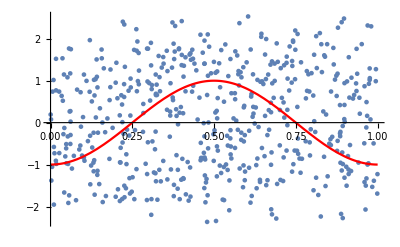

```mathematica
b2=BetaDistribution[1,1];
g2= MultinormalDistribution[{2.5,0},{{0.1,0.0},{0.0,0.3}}];
guess = Mean[ProductDistribution[b2,g2]]
Show[plot1@guess[[2]],plot2@@guess[[{3,1}]]]
n = 100000;
```

0.482709

BetaDistribution[2803.74,967.824]

MultinormalDistribution[{2.77243,0.394486},{{1.40746×10^-8,-4.4381×10^-8},{-4.4381×10^-8,0.000389997}}]

{0.743389,2.77243,0.394486}

{15.9975,1.48362}

{0.00711094,0.000118637,0.0197484}

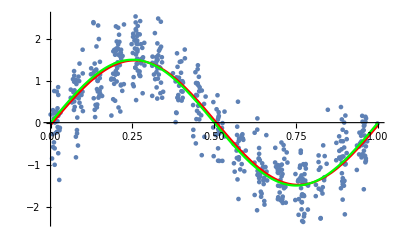

```mathematica
(* Goofy iteration here *)
xx = RandomVariate[ProductDistribution[b2,g2],n];
lik = chi2@@@xx;
lik = lik-Min[lik];
lik = Exp[-lik/2];
pp = PDF[b2,xx[[All,1]]]*PDF[g2,xx[[All,2;;3]]];
wt = lik/pp;
wt = wt/Total[wt];
(* Compute perplexity *)
Exp[- Total[wt Log[wt]]]/n
(* Update distributions *)
b2 = EstimatedDistribution[WeightedData[xx[[All,1]],wt],BetaDistribution[a1,b1]]
g2=EstimatedDistribution[WeightedData[xx[[All,2;;3]],wt],MultinormalDistribution[{m1,m2},{{c11,c12},{c21,c22}}]]
guess= Mean[ProductDistribution[b2,g2]]
Exp[guess[[2;;]]]
StandardDeviation[ProductDistribution[b2,g2]]
Show[plot1@guess[[2]],plot2@@guess[[{3,1}]],plot2[Log[1.5],0.75,Green]]
```